## Cadena

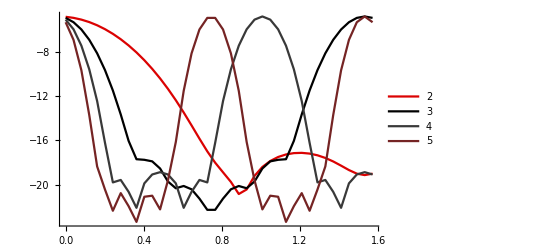

```mathematica
datos="/home/amaro/doc/carlos/cadena/datos6/";
ϕ={0.,0.04027683,0.08055366,0.12083049,0.16110732,0.20138414,0.24166097,0.2819378,0.32221463,0.36249146,0.40276829,0.44304512,0.48332195,0.52359878,0.5638756,0.60415243,0.64442926,0.68470609,0.72498292,0.76525975,0.80553658,0.84581341,0.88609024,0.92636706,0.96664389,1.00692072,1.04719755,1.08747438,1.12775121,1.16802804,1.20830487,1.2485817,1.28885852,1.32913535,1.36941218,1.40968901,1.44996584,1.49024267,1.5305195,1.57079633};
masmatrices=Table[Import[datos<>"papa"<>ToString[i-1]<>".dat","Table"],{i,1,40}]/2^8;
eldichoso=Table[Flatten[Table[Log[10,Abs[masmatrices[[k]][[i]]]^2],{i,1,40}]],{k,1,40}];
graficas=Table[ListLinePlot[Table[{ϕ[[i]],eldichoso[[k]][[i]]},{i,1,40}],Filling->False,PlotLegends->{ToString[k]},PlotStyle->k],{k,2,5}];
Show[graficas,PlotRange->All]
```

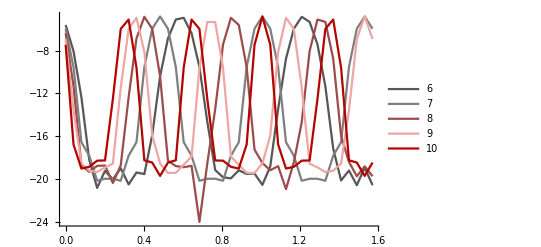

```mathematica
graficas=Table[ListLinePlot[Table[{ϕ[[i]],eldichoso[[k]][[i]]},{i,1,40}],Filling->False,PlotLegends->{ToString[k]},PlotStyle->k],{k,6,10}];
Show[graficas,PlotRange->All]
```

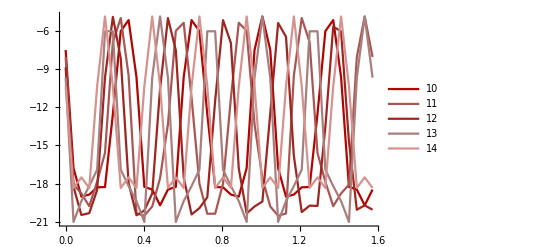

```mathematica
graficas=Table[ListLinePlot[Table[{ϕ[[i]],eldichoso[[k]][[i]]},{i,1,40}],Filling->False,PlotLegends->{ToString[k]},PlotStyle->k],{k,10,14}];
Show[graficas,PlotRange->All]
```

## Malla de 5x5

```mathematica
trazas2=Table[Import[datos<>"chin_"<>ToString[i-1]<>".dat","Table"],{i,1,12}]/2^25;
```

```mathematica
eldichoso2=Table[Flatten[Table[Log[10,Abs[trazas2[[k]][[i]]]^2],{i,1,40}]],{k,1,12}];
graficas=Table[ListLinePlot[Table[{ϕ[[i]],eldichoso2[[k]][[i]]},{i,1,40}],Filling->False,PlotLegends->{ToString[k]},PlotStyle->k],{k,2,5}];
```

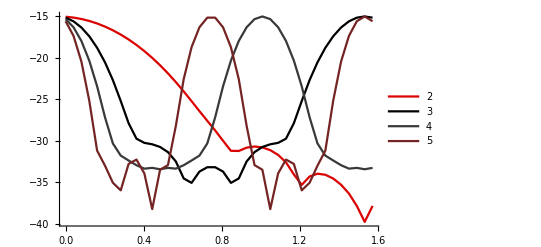

```mathematica
Show[graficas,PlotRange->All]
```

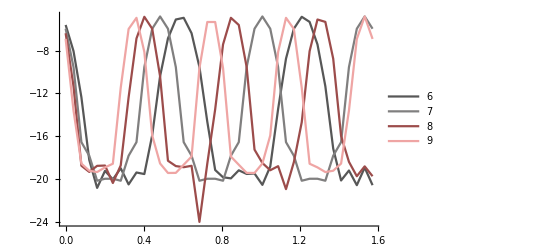

```mathematica
graficas=Table[ListLinePlot[Table[{ϕ[[i]],eldichoso[[k]][[i]]},{i,1,40}],Filling->False,PlotLegends->{ToString[k]},PlotStyle->k],{k,6,9}];
Show[graficas,PlotRange->All]
```

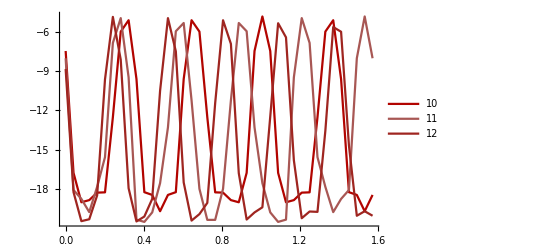

```mathematica
graficas=Table[ListLinePlot[Table[{ϕ[[i]],eldichoso[[k]][[i]]},{i,1,40}],Filling->False,PlotLegends->{ToString[k]},PlotStyle->k],{k,10,12}];
Show[graficas,PlotRange->All]
```